```mathematica
A=1/Sqrt[2];
B=1/Sqrt[2];
delta=Pi/2;
alpha = 1/2*ArcTan[(2*A*B*Cos[delta])/(A^2-B^2)];
Ealpha=Sqrt[A^2*Cos[alpha]^2+B^2*(Sin[alpha])^2+A*B*Cos[delta]*Sin[2*alpha]]
Ealphapi=Sqrt[A^2*Cos[alpha]^2+B^2*(Sin[alpha])^2-A*B*Cos[delta]*Sin[2*alpha]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression (0 ComplexInfinity)/(√2 √2) encountered.

Indeterminate

Indeterminate

```mathematica
N[Ealpha]
N[Ealphapi]
```

√(0.5 Cos[alpha]^2+0.5 Sin[alpha]^2+0.5 Sin[2. alpha])

√(0.5 Cos[alpha]^2+0.5 Sin[alpha]^2-0.5 Sin[2. alpha])

## Problem 5.8

```mathematica
bright={{17,2*Pi},{30,4*Pi},{38,6*Pi},{46,8*Pi},{55,10*Pi},{62,12*Pi},{71,14*Pi}};
dim={{0,0},{24,3*Pi},{34,5*Pi},{43,7*Pi},{51,9*Pi},{59,11*Pi},{66,13*Pi}};
```

```mathematica
combineddata={{0,0},{17,2*Pi},{24,3*Pi},{30,4*Pi},{34,5*Pi},{38,6*Pi},{43,7*Pi},{46,8*Pi},{51,9*Pi},{55,10*Pi},{59,11*Pi},{62,12*Pi},{66,13*Pi},{71,14*Pi}};
```

```mathematica
fitcombined=Fit[combineddata,{1,x,x^2},x]
```

-0.573115+0.341782 x+0.0042717 x^2

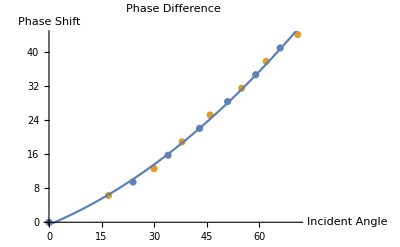

```mathematica
Show[ListPlot[{dim,bright},PlotLabel->"Phase Difference",AxesLabel->{"Incident Angle","Phase Shift"}],Plot[fitcombined,{x,0,90}]]
```

```mathematica
(* Notice how the dots start as a parabola and then begin to flatten out at about 15*Pi or 90 degrees *)
```